```mathematica
Clear[Subscript](*只有这个可以清除带下标的变量*)

Subscript[k, x]=k
Subscript[k, y]=0
Subscript[k, z]=0
A=Det[({{Subscript[β, 1]*(4-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]-Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]-Cos[a/2*(Subscript[k, x]-Subscript[k, y])])+2β-m*w^2, Subscript[β, 1]*(Cos[a/2*(Subscript[k, x]-Subscript[k, y])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]), Subscript[β, 1]*(Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]), -2*β*Cos[a/2*Subscript[k, x]], 0, 0}, {Subscript[β, 1]*(Cos[a/2*(Subscript[k, x]-Subscript[k, y])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]), Subscript[β, 1]*(4-Cos[a/2*(Subscript[k, y]+Subscript[k, z])]-Cos[a/2*(Subscript[k, y]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]-Cos[a/2*(Subscript[k, x]-Subscript[k, y])])+2β-m*w^2, Subscript[β, 1]*(Cos[a/2*(Subscript[k, z]-Subscript[k, y])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]), 0, -2*β*Cos[a/2*Subscript[k, y]], 0}, {Subscript[β, 1]*(Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]), Subscript[β, 1]*(Cos[a/2*(Subscript[k, z]-Subscript[k, y])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]), Subscript[β, 1]*(4-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]-Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]-Cos[a/2*(Subscript[k, z]-Subscript[k, y])])+2β-m*w^2, 0, 0, -2*β*Cos[a/2*Subscript[k, z]]}, {-2*β*Cos[a/2*Subscript[k, x]], 0, 0, Subscript[β, 2]*(4-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]-Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]-Cos[a/2*(Subscript[k, x]-Subscript[k, y])])+2β-M*w^2, Subscript[β, 2]*(Cos[a/2*(Subscript[k, x]-Subscript[k, y])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]), Subscript[β, 2]*(Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, z])])}, {0, -2*β*Cos[a/2*Subscript[k, y]], 0, Subscript[β, 2]*(Cos[a/2*(Subscript[k, x]-Subscript[k, y])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]), Subscript[β, 2]*(4-Cos[a/2*(Subscript[k, y]+Subscript[k, z])]-Cos[a/2*(Subscript[k, y]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]-Cos[a/2*(Subscript[k, x]-Subscript[k, y])])+2β-M*w^2, Subscript[β, 2]*(Cos[a/2*(Subscript[k, z]-Subscript[k, y])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])])}, {0, 0, -2*β*Cos[a/2*Subscript[k, z]], Subscript[β, 2]*(Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]), Subscript[β, 2]*(Cos[a/2*(Subscript[k, z]-Subscript[k, y])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]), Subscript[β, 2]*(4-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]-Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]-Cos[a/2*(Subscript[k, z]-Subscript[k, y])])+2β-M*w^2}})]
Solve[A==0,w]
```

k

0

0

-4 β^2 (-4 β^2 (-4 β^2 Cos[(a k)/2]^2+(-m w^2+2 β+(4-4 Cos[(a k)/2]) β_1) (-M w^2+2 β+(4-4 Cos[(a k)/2]) β_2))+(-m w^2+2 β+(2-2 Cos[(a k)/2]) β_1) (-M w^2+2 β+(2-2 Cos[(a k)/2]) β_2) (-4 β^2 Cos[(a k)/2]^2+(-m w^2+2 β+(4-4 Cos[(a k)/2]) β_1) (-M w^2+2 β+(4-4 Cos[(a k)/2]) β_2)))+(-m w^2+2 β+(2-2 Cos[(a k)/2]) β_1) (-M w^2+2 β+(2-2 Cos[(a k)/2]) β_2) (-4 β^2 (-4 β^2 Cos[(a k)/2]^2+(-m w^2+2 β+(4-4 Cos[(a k)/2]) β_1) (-M w^2+2 β+(4-4 Cos[(a k)/2]) β_2))+(-m w^2+2 β+(2-2 Cos[(a k)/2]) β_1) (-M w^2+2 β+(2-2 Cos[(a k)/2]) β_2) (-4 β^2 Cos[(a k)/2]^2+(-m w^2+2 β+(4-4 Cos[(a k)/2]) β_1) (-M w^2+2 β+(4-4 Cos[(a k)/2]) β_2)))

{{w→-√(β/m+β/M+β_1/m-(Cos[(a k)/2] β_1)/m+β_2/M-(Cos[(a k)/2] β_2)/M-(√((-2 m β-2 M β-2 M β_1+2 M Cos[(a k)/2] β_1-2 m β_2+2 m Cos[(a k)/2] β_2)^2-4 m M (4 β β_1-4 β Cos[(a k)/2] β_1+4 β β_2-4 β Cos[(a k)/2] β_2+6 β_1 β_2-8 Cos[(a k)/2] β_1 β_2+2 Cos[a k] β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+β_1/m-(Cos[(a k)/2] β_1)/m+β_2/M-(Cos[(a k)/2] β_2)/M-(√((-2 m β-2 M β-2 M β_1+2 M Cos[(a k)/2] β_1-2 m β_2+2 m Cos[(a k)/2] β_2)^2-4 m M (4 β β_1-4 β Cos[(a k)/2] β_1+4 β β_2-4 β Cos[(a k)/2] β_2+6 β_1 β_2-8 Cos[(a k)/2] β_1 β_2+2 Cos[a k] β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+β_1/m-(Cos[(a k)/2] β_1)/m+β_2/M-(Cos[(a k)/2] β_2)/M-(√((-2 m β-2 M β-2 M β_1+2 M Cos[(a k)/2] β_1-2 m β_2+2 m Cos[(a k)/2] β_2)^2-4 m M (4 β β_1-4 β Cos[(a k)/2] β_1+4 β β_2-4 β Cos[(a k)/2] β_2+6 β_1 β_2-8 Cos[(a k)/2] β_1 β_2+2 Cos[a k] β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+β_1/m-(Cos[(a k)/2] β_1)/m+β_2/M-(Cos[(a k)/2] β_2)/M-(√((-2 m β-2 M β-2 M β_1+2 M Cos[(a k)/2] β_1-2 m β_2+2 m Cos[(a k)/2] β_2)^2-4 m M (4 β β_1-4 β Cos[(a k)/2] β_1+4 β β_2-4 β Cos[(a k)/2] β_2+6 β_1 β_2-8 Cos[(a k)/2] β_1 β_2+2 Cos[a k] β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+β_1/m-(Cos[(a k)/2] β_1)/m+β_2/M-(Cos[(a k)/2] β_2)/M+(√((-2 m β-2 M β-2 M β_1+2 M Cos[(a k)/2] β_1-2 m β_2+2 m Cos[(a k)/2] β_2)^2-4 m M (4 β β_1-4 β Cos[(a k)/2] β_1+4 β β_2-4 β Cos[(a k)/2] β_2+6 β_1 β_2-8 Cos[(a k)/2] β_1 β_2+2 Cos[a k] β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+β_1/m-(Cos[(a k)/2] β_1)/m+β_2/M-(Cos[(a k)/2] β_2)/M+(√((-2 m β-2 M β-2 M β_1+2 M Cos[(a k)/2] β_1-2 m β_2+2 m Cos[(a k)/2] β_2)^2-4 m M (4 β β_1-4 β Cos[(a k)/2] β_1+4 β β_2-4 β Cos[(a k)/2] β_2+6 β_1 β_2-8 Cos[(a k)/2] β_1 β_2+2 Cos[a k] β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+β_1/m-(Cos[(a k)/2] β_1)/m+β_2/M-(Cos[(a k)/2] β_2)/M+(√((-2 m β-2 M β-2 M β_1+2 M Cos[(a k)/2] β_1-2 m β_2+2 m Cos[(a k)/2] β_2)^2-4 m M (4 β β_1-4 β Cos[(a k)/2] β_1+4 β β_2-4 β Cos[(a k)/2] β_2+6 β_1 β_2-8 Cos[(a k)/2] β_1 β_2+2 Cos[a k] β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+β_1/m-(Cos[(a k)/2] β_1)/m+β_2/M-(Cos[(a k)/2] β_2)/M+(√((-2 m β-2 M β-2 M β_1+2 M Cos[(a k)/2] β_1-2 m β_2+2 m Cos[(a k)/2] β_2)^2-4 m M (4 β β_1-4 β Cos[(a k)/2] β_1+4 β β_2-4 β Cos[(a k)/2] β_2+6 β_1 β_2-8 Cos[(a k)/2] β_1 β_2+2 Cos[a k] β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+(2 β_1)/m-(2 Cos[(a k)/2] β_1)/m+(2 β_2)/M-(2 Cos[(a k)/2] β_2)/M-(√((-2 m β-2 M β-4 M β_1+4 M Cos[(a k)/2] β_1-4 m β_2+4 m Cos[(a k)/2] β_2)^2-4 m M (2 β^2-2 β^2 Cos[a k]+8 β β_1-8 β Cos[(a k)/2] β_1+8 β β_2-8 β Cos[(a k)/2] β_2+24 β_1 β_2-32 Cos[(a k)/2] β_1 β_2+8 Cos[a k] β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+(2 β_1)/m-(2 Cos[(a k)/2] β_1)/m+(2 β_2)/M-(2 Cos[(a k)/2] β_2)/M-(√((-2 m β-2 M β-4 M β_1+4 M Cos[(a k)/2] β_1-4 m β_2+4 m Cos[(a k)/2] β_2)^2-4 m M (2 β^2-2 β^2 Cos[a k]+8 β β_1-8 β Cos[(a k)/2] β_1+8 β β_2-8 β Cos[(a k)/2] β_2+24 β_1 β_2-32 Cos[(a k)/2] β_1 β_2+8 Cos[a k] β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+(2 β_1)/m-(2 Cos[(a k)/2] β_1)/m+(2 β_2)/M-(2 Cos[(a k)/2] β_2)/M+(√((-2 m β-2 M β-4 M β_1+4 M Cos[(a k)/2] β_1-4 m β_2+4 m Cos[(a k)/2] β_2)^2-4 m M (2 β^2-2 β^2 Cos[a k]+8 β β_1-8 β Cos[(a k)/2] β_1+8 β β_2-8 β Cos[(a k)/2] β_2+24 β_1 β_2-32 Cos[(a k)/2] β_1 β_2+8 Cos[a k] β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+(2 β_1)/m-(2 Cos[(a k)/2] β_1)/m+(2 β_2)/M-(2 Cos[(a k)/2] β_2)/M+(√((-2 m β-2 M β-4 M β_1+4 M Cos[(a k)/2] β_1-4 m β_2+4 m Cos[(a k)/2] β_2)^2-4 m M (2 β^2-2 β^2 Cos[a k]+8 β β_1-8 β Cos[(a k)/2] β_1+8 β β_2-8 β Cos[(a k)/2] β_2+24 β_1 β_2-32 Cos[(a k)/2] β_1 β_2+8 Cos[a k] β_1 β_2)))/(2 m M))}}

```mathematica
Clear[Subscript](*只有这个可以清除带下标的变量*)

Subscript[k, x]=k/(√3)
Subscript[k, y]=k/(√3)
Subscript[k, z]=k/(√3)
A=Det[({{Subscript[β, 1]*(4-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]-Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]-Cos[a/2*(Subscript[k, x]-Subscript[k, y])])+2β-m*w^2, Subscript[β, 1]*(Cos[a/2*(Subscript[k, x]-Subscript[k, y])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]), Subscript[β, 1]*(Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]), -2*β*Cos[a/2*Subscript[k, x]], 0, 0}, {Subscript[β, 1]*(Cos[a/2*(Subscript[k, x]-Subscript[k, y])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]), Subscript[β, 1]*(4-Cos[a/2*(Subscript[k, y]+Subscript[k, z])]-Cos[a/2*(Subscript[k, y]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]-Cos[a/2*(Subscript[k, x]-Subscript[k, y])])+2β-m*w^2, Subscript[β, 1]*(Cos[a/2*(Subscript[k, z]-Subscript[k, y])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]), 0, -2*β*Cos[a/2*Subscript[k, y]], 0}, {Subscript[β, 1]*(Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]), Subscript[β, 1]*(Cos[a/2*(Subscript[k, z]-Subscript[k, y])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]), Subscript[β, 1]*(4-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]-Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]-Cos[a/2*(Subscript[k, z]-Subscript[k, y])])+2β-m*w^2, 0, 0, -2*β*Cos[a/2*Subscript[k, z]]}, {-2*β*Cos[a/2*Subscript[k, x]], 0, 0, Subscript[β, 2]*(4-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]-Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]-Cos[a/2*(Subscript[k, x]-Subscript[k, y])])+2β-M*w^2, Subscript[β, 2]*(Cos[a/2*(Subscript[k, x]-Subscript[k, y])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]), Subscript[β, 2]*(Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, z])])}, {0, -2*β*Cos[a/2*Subscript[k, y]], 0, Subscript[β, 2]*(Cos[a/2*(Subscript[k, x]-Subscript[k, y])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]), Subscript[β, 2]*(4-Cos[a/2*(Subscript[k, y]+Subscript[k, z])]-Cos[a/2*(Subscript[k, y]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, y])]-Cos[a/2*(Subscript[k, x]-Subscript[k, y])])+2β-M*w^2, Subscript[β, 2]*(Cos[a/2*(Subscript[k, z]-Subscript[k, y])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])])}, {0, 0, -2*β*Cos[a/2*Subscript[k, z]], Subscript[β, 2]*(Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]), Subscript[β, 2]*(Cos[a/2*(Subscript[k, z]-Subscript[k, y])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]), Subscript[β, 2]*(4-Cos[a/2*(Subscript[k, x]+Subscript[k, z])]-Cos[a/2*(Subscript[k, x]-Subscript[k, z])]-Cos[a/2*(Subscript[k, z]+Subscript[k, y])]-Cos[a/2*(Subscript[k, z]-Subscript[k, y])])+2β-M*w^2}})]
Solve[A==0,w]
```

k/(√3)

k/(√3)

k/(√3)

(1-Cos[(a k)/(√3)]) β_2 (-(-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2) (-4 β^2 Cos[(a k)/(2 √3)]^2 (m w^2 β_1-2 β β_1-m w^2 Cos[(a k)/(√3)] β_1+2 β Cos[(a k)/(√3)] β_1-β_1^2+2 Cos[(a k)/(√3)] β_1^2-Cos[(a k)/(√3)]^2 β_1^2)+(1-Cos[(a k)/(√3)]) (-m^3 w^6+6 m^2 w^4 β-12 m w^2 β^2+8 β^3+6 m^2 w^4 β_1-24 m w^2 β β_1+24 β^2 β_1-6 m^2 w^4 Cos[(a k)/(√3)] β_1+24 m w^2 β Cos[(a k)/(√3)] β_1-24 β^2 Cos[(a k)/(√3)] β_1-9 m w^2 β_1^2+18 β β_1^2+18 m w^2 Cos[(a k)/(√3)] β_1^2-36 β Cos[(a k)/(√3)] β_1^2-9 m w^2 Cos[(a k)/(√3)]^2 β_1^2+18 β Cos[(a k)/(√3)]^2 β_1^2+4 β_1^3-12 Cos[(a k)/(√3)] β_1^3+12 Cos[(a k)/(√3)]^2 β_1^3-4 Cos[(a k)/(√3)]^3 β_1^3) β_2)+(1-Cos[(a k)/(√3)]) β_2 (4 β^2 Cos[(a k)/(2 √3)]^2 (-m w^2 β_1+2 β β_1+m w^2 Cos[(a k)/(√3)] β_1-2 β Cos[(a k)/(√3)] β_1+β_1^2-2 Cos[(a k)/(√3)] β_1^2+Cos[(a k)/(√3)]^2 β_1^2)+(1-Cos[(a k)/(√3)]) (-m^3 w^6+6 m^2 w^4 β-12 m w^2 β^2+8 β^3+6 m^2 w^4 β_1-24 m w^2 β β_1+24 β^2 β_1-6 m^2 w^4 Cos[(a k)/(√3)] β_1+24 m w^2 β Cos[(a k)/(√3)] β_1-24 β^2 Cos[(a k)/(√3)] β_1-9 m w^2 β_1^2+18 β β_1^2+18 m w^2 Cos[(a k)/(√3)] β_1^2-36 β Cos[(a k)/(√3)] β_1^2-9 m w^2 Cos[(a k)/(√3)]^2 β_1^2+18 β Cos[(a k)/(√3)]^2 β_1^2+4 β_1^3-12 Cos[(a k)/(√3)] β_1^3+12 Cos[(a k)/(√3)]^2 β_1^3-4 Cos[(a k)/(√3)]^3 β_1^3) β_2)+2 β Cos[(a k)/(2 √3)] (2 β Cos[(a k)/(2 √3)] (1-Cos[(a k)/(√3)]) (-(1-Cos[(a k)/(√3)])^2 β_1^2+(-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1)^2) β_2+2 β Cos[(a k)/(2 √3)] (4 β^2 Cos[(a k)/(2 √3)]^2 β_1-4 β^2 Cos[(a k)/(2 √3)]^2 Cos[(a k)/(√3)] β_1-m w^2 β_1 β_2+2 β β_1 β_2+2 m w^2 Cos[(a k)/(√3)] β_1 β_2-4 β Cos[(a k)/(√3)] β_1 β_2-m w^2 Cos[(a k)/(√3)]^2 β_1 β_2+2 β Cos[(a k)/(√3)]^2 β_1 β_2+β_1^2 β_2-3 Cos[(a k)/(√3)] β_1^2 β_2+3 Cos[(a k)/(√3)]^2 β_1^2 β_2-Cos[(a k)/(√3)]^3 β_1^2 β_2)))-(1-Cos[(a k)/(√3)]) β_2 (-(1-Cos[(a k)/(√3)]) β_2 (-4 β^2 Cos[(a k)/(2 √3)]^2 (m w^2 β_1-2 β β_1-m w^2 Cos[(a k)/(√3)] β_1+2 β Cos[(a k)/(√3)] β_1-β_1^2+2 Cos[(a k)/(√3)] β_1^2-Cos[(a k)/(√3)]^2 β_1^2)+(1-Cos[(a k)/(√3)]) (-m^3 w^6+6 m^2 w^4 β-12 m w^2 β^2+8 β^3+6 m^2 w^4 β_1-24 m w^2 β β_1+24 β^2 β_1-6 m^2 w^4 Cos[(a k)/(√3)] β_1+24 m w^2 β Cos[(a k)/(√3)] β_1-24 β^2 Cos[(a k)/(√3)] β_1-9 m w^2 β_1^2+18 β β_1^2+18 m w^2 Cos[(a k)/(√3)] β_1^2-36 β Cos[(a k)/(√3)] β_1^2-9 m w^2 Cos[(a k)/(√3)]^2 β_1^2+18 β Cos[(a k)/(√3)]^2 β_1^2+4 β_1^3-12 Cos[(a k)/(√3)] β_1^3+12 Cos[(a k)/(√3)]^2 β_1^3-4 Cos[(a k)/(√3)]^3 β_1^3) β_2)+(1-Cos[(a k)/(√3)]) β_2 (-4 β^2 Cos[(a k)/(2 √3)]^2 (-(1-Cos[(a k)/(√3)])^2 β_1^2+(-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1)^2)+(-m^3 w^6+6 m^2 w^4 β-12 m w^2 β^2+8 β^3+6 m^2 w^4 β_1-24 m w^2 β β_1+24 β^2 β_1-6 m^2 w^4 Cos[(a k)/(√3)] β_1+24 m w^2 β Cos[(a k)/(√3)] β_1-24 β^2 Cos[(a k)/(√3)] β_1-9 m w^2 β_1^2+18 β β_1^2+18 m w^2 Cos[(a k)/(√3)] β_1^2-36 β Cos[(a k)/(√3)] β_1^2-9 m w^2 Cos[(a k)/(√3)]^2 β_1^2+18 β Cos[(a k)/(√3)]^2 β_1^2+4 β_1^3-12 Cos[(a k)/(√3)] β_1^3+12 Cos[(a k)/(√3)]^2 β_1^3-4 Cos[(a k)/(√3)]^3 β_1^3) (-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2))+2 β Cos[(a k)/(2 √3)] (-2 β Cos[(a k)/(2 √3)] (1-Cos[(a k)/(√3)]) (-m w^2 β_1+2 β β_1+m w^2 Cos[(a k)/(√3)] β_1-2 β Cos[(a k)/(√3)] β_1+β_1^2-2 Cos[(a k)/(√3)] β_1^2+Cos[(a k)/(√3)]^2 β_1^2) β_2+2 β Cos[(a k)/(2 √3)] (-2 β Cos[(a k)/(2 √3)] (2 β Cos[(a k)/(2 √3)] β_1-2 β Cos[(a k)/(2 √3)] Cos[(a k)/(√3)] β_1)+(-m w^2 β_1+2 β β_1+m w^2 Cos[(a k)/(√3)] β_1-2 β Cos[(a k)/(√3)] β_1+β_1^2-2 Cos[(a k)/(√3)] β_1^2+Cos[(a k)/(√3)]^2 β_1^2) (-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2))))+(-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2) (-(1-Cos[(a k)/(√3)]) β_2 (4 β^2 Cos[(a k)/(2 √3)]^2 (-m w^2 β_1+2 β β_1+m w^2 Cos[(a k)/(√3)] β_1-2 β Cos[(a k)/(√3)] β_1+β_1^2-2 Cos[(a k)/(√3)] β_1^2+Cos[(a k)/(√3)]^2 β_1^2)+(1-Cos[(a k)/(√3)]) (-m^3 w^6+6 m^2 w^4 β-12 m w^2 β^2+8 β^3+6 m^2 w^4 β_1-24 m w^2 β β_1+24 β^2 β_1-6 m^2 w^4 Cos[(a k)/(√3)] β_1+24 m w^2 β Cos[(a k)/(√3)] β_1-24 β^2 Cos[(a k)/(√3)] β_1-9 m w^2 β_1^2+18 β β_1^2+18 m w^2 Cos[(a k)/(√3)] β_1^2-36 β Cos[(a k)/(√3)] β_1^2-9 m w^2 Cos[(a k)/(√3)]^2 β_1^2+18 β Cos[(a k)/(√3)]^2 β_1^2+4 β_1^3-12 Cos[(a k)/(√3)] β_1^3+12 Cos[(a k)/(√3)]^2 β_1^3-4 Cos[(a k)/(√3)]^3 β_1^3) β_2)+(-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2) (-4 β^2 Cos[(a k)/(2 √3)]^2 (-(1-Cos[(a k)/(√3)])^2 β_1^2+(-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1)^2)+(-m^3 w^6+6 m^2 w^4 β-12 m w^2 β^2+8 β^3+6 m^2 w^4 β_1-24 m w^2 β β_1+24 β^2 β_1-6 m^2 w^4 Cos[(a k)/(√3)] β_1+24 m w^2 β Cos[(a k)/(√3)] β_1-24 β^2 Cos[(a k)/(√3)] β_1-9 m w^2 β_1^2+18 β β_1^2+18 m w^2 Cos[(a k)/(√3)] β_1^2-36 β Cos[(a k)/(√3)] β_1^2-9 m w^2 Cos[(a k)/(√3)]^2 β_1^2+18 β Cos[(a k)/(√3)]^2 β_1^2+4 β_1^3-12 Cos[(a k)/(√3)] β_1^3+12 Cos[(a k)/(√3)]^2 β_1^3-4 Cos[(a k)/(√3)]^3 β_1^3) (-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2))+2 β Cos[(a k)/(2 √3)] (-2 β Cos[(a k)/(2 √3)] (1-Cos[(a k)/(√3)]) (-m w^2 β_1+2 β β_1+m w^2 Cos[(a k)/(√3)] β_1-2 β Cos[(a k)/(√3)] β_1+β_1^2-2 Cos[(a k)/(√3)] β_1^2+Cos[(a k)/(√3)]^2 β_1^2) β_2-2 β Cos[(a k)/(2 √3)] (-4 β^2 Cos[(a k)/(2 √3)]^2 (-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1)+(-(1-Cos[(a k)/(√3)])^2 β_1^2+(-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1)^2) (-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2))))+2 β Cos[(a k)/(2 √3)] (-(1-Cos[(a k)/(√3)]) β_2 (-2 β Cos[(a k)/(2 √3)] (m w^2 β_1-2 β β_1-m w^2 Cos[(a k)/(√3)] β_1+2 β Cos[(a k)/(√3)] β_1-β_1^2+2 Cos[(a k)/(√3)] β_1^2-Cos[(a k)/(√3)]^2 β_1^2) (-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2)-2 β Cos[(a k)/(2 √3)] (4 β^2 Cos[(a k)/(2 √3)]^2 β_1-4 β^2 Cos[(a k)/(2 √3)]^2 Cos[(a k)/(√3)] β_1-m w^2 β_1 β_2+2 β β_1 β_2+2 m w^2 Cos[(a k)/(√3)] β_1 β_2-4 β Cos[(a k)/(√3)] β_1 β_2-m w^2 Cos[(a k)/(√3)]^2 β_1 β_2+2 β Cos[(a k)/(√3)]^2 β_1 β_2+β_1^2 β_2-3 Cos[(a k)/(√3)] β_1^2 β_2+3 Cos[(a k)/(√3)]^2 β_1^2 β_2-Cos[(a k)/(√3)]^3 β_1^2 β_2))+(1-Cos[(a k)/(√3)]) β_2 (-2 β Cos[(a k)/(2 √3)] (1-Cos[(a k)/(√3)]) (m w^2 β_1-2 β β_1-m w^2 Cos[(a k)/(√3)] β_1+2 β Cos[(a k)/(√3)] β_1-β_1^2+2 Cos[(a k)/(√3)] β_1^2-Cos[(a k)/(√3)]^2 β_1^2) β_2-2 β Cos[(a k)/(2 √3)] (-2 β Cos[(a k)/(2 √3)] (2 β Cos[(a k)/(2 √3)] β_1-2 β Cos[(a k)/(2 √3)] Cos[(a k)/(√3)] β_1)+(-m w^2 β_1+2 β β_1+m w^2 Cos[(a k)/(√3)] β_1-2 β Cos[(a k)/(√3)] β_1+β_1^2-2 Cos[(a k)/(√3)] β_1^2+Cos[(a k)/(√3)]^2 β_1^2) (-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2)))-2 β Cos[(a k)/(2 √3)] (-(1-Cos[(a k)/(√3)]) β_2 (-2 β Cos[(a k)/(2 √3)] (-2 β Cos[(a k)/(2 √3)] β_1+2 β Cos[(a k)/(2 √3)] Cos[(a k)/(√3)] β_1)+(1-Cos[(a k)/(√3)]) (-(1-Cos[(a k)/(√3)])^2 β_1^2+(-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1)^2) β_2)+(-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2) (-4 β^2 Cos[(a k)/(2 √3)]^2 (-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1)+(-(1-Cos[(a k)/(√3)])^2 β_1^2+(-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1)^2) (-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2))-2 β Cos[(a k)/(2 √3)] ((1-Cos[(a k)/(√3)]) (2 β Cos[(a k)/(2 √3)] β_1-2 β Cos[(a k)/(2 √3)] Cos[(a k)/(√3)] β_1) β_2+2 β Cos[(a k)/(2 √3)] (-4 β^2 Cos[(a k)/(2 √3)]^2+(-m w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_1) (-M w^2+2 β+(2-2 Cos[(a k)/(√3)]) β_2)))))

{{w→-√(β/m+β/M+β_1/(2 m)-(Cos[(a k)/(√3)] β_1)/(2 m)+β_2/(2 M)-(Cos[(a k)/(√3)] β_2)/(2 M)-(√((-2 m β-2 M β-M β_1+M Cos[(a k)/(√3)] β_1-m β_2+m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β β_1-2 β Cos[(a k)/(√3)] β_1+2 β β_2-2 β Cos[(a k)/(√3)] β_2+β_1 β_2-2 Cos[(a k)/(√3)] β_1 β_2+Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+β_1/(2 m)-(Cos[(a k)/(√3)] β_1)/(2 m)+β_2/(2 M)-(Cos[(a k)/(√3)] β_2)/(2 M)-(√((-2 m β-2 M β-M β_1+M Cos[(a k)/(√3)] β_1-m β_2+m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β β_1-2 β Cos[(a k)/(√3)] β_1+2 β β_2-2 β Cos[(a k)/(√3)] β_2+β_1 β_2-2 Cos[(a k)/(√3)] β_1 β_2+Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+β_1/(2 m)-(Cos[(a k)/(√3)] β_1)/(2 m)+β_2/(2 M)-(Cos[(a k)/(√3)] β_2)/(2 M)-(√((-2 m β-2 M β-M β_1+M Cos[(a k)/(√3)] β_1-m β_2+m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β β_1-2 β Cos[(a k)/(√3)] β_1+2 β β_2-2 β Cos[(a k)/(√3)] β_2+β_1 β_2-2 Cos[(a k)/(√3)] β_1 β_2+Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+β_1/(2 m)-(Cos[(a k)/(√3)] β_1)/(2 m)+β_2/(2 M)-(Cos[(a k)/(√3)] β_2)/(2 M)-(√((-2 m β-2 M β-M β_1+M Cos[(a k)/(√3)] β_1-m β_2+m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β β_1-2 β Cos[(a k)/(√3)] β_1+2 β β_2-2 β Cos[(a k)/(√3)] β_2+β_1 β_2-2 Cos[(a k)/(√3)] β_1 β_2+Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+β_1/(2 m)-(Cos[(a k)/(√3)] β_1)/(2 m)+β_2/(2 M)-(Cos[(a k)/(√3)] β_2)/(2 M)+(√((-2 m β-2 M β-M β_1+M Cos[(a k)/(√3)] β_1-m β_2+m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β β_1-2 β Cos[(a k)/(√3)] β_1+2 β β_2-2 β Cos[(a k)/(√3)] β_2+β_1 β_2-2 Cos[(a k)/(√3)] β_1 β_2+Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+β_1/(2 m)-(Cos[(a k)/(√3)] β_1)/(2 m)+β_2/(2 M)-(Cos[(a k)/(√3)] β_2)/(2 M)+(√((-2 m β-2 M β-M β_1+M Cos[(a k)/(√3)] β_1-m β_2+m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β β_1-2 β Cos[(a k)/(√3)] β_1+2 β β_2-2 β Cos[(a k)/(√3)] β_2+β_1 β_2-2 Cos[(a k)/(√3)] β_1 β_2+Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+β_1/(2 m)-(Cos[(a k)/(√3)] β_1)/(2 m)+β_2/(2 M)-(Cos[(a k)/(√3)] β_2)/(2 M)+(√((-2 m β-2 M β-M β_1+M Cos[(a k)/(√3)] β_1-m β_2+m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β β_1-2 β Cos[(a k)/(√3)] β_1+2 β β_2-2 β Cos[(a k)/(√3)] β_2+β_1 β_2-2 Cos[(a k)/(√3)] β_1 β_2+Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+β_1/(2 m)-(Cos[(a k)/(√3)] β_1)/(2 m)+β_2/(2 M)-(Cos[(a k)/(√3)] β_2)/(2 M)+(√((-2 m β-2 M β-M β_1+M Cos[(a k)/(√3)] β_1-m β_2+m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β β_1-2 β Cos[(a k)/(√3)] β_1+2 β β_2-2 β Cos[(a k)/(√3)] β_2+β_1 β_2-2 Cos[(a k)/(√3)] β_1 β_2+Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+(2 β_1)/m-(2 Cos[(a k)/(√3)] β_1)/m+(2 β_2)/M-(2 Cos[(a k)/(√3)] β_2)/M-(√((-2 m β-2 M β-4 M β_1+4 M Cos[(a k)/(√3)] β_1-4 m β_2+4 m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+8 β β_1-8 β Cos[(a k)/(√3)] β_1+8 β β_2-8 β Cos[(a k)/(√3)] β_2+16 β_1 β_2-32 Cos[(a k)/(√3)] β_1 β_2+16 Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+(2 β_1)/m-(2 Cos[(a k)/(√3)] β_1)/m+(2 β_2)/M-(2 Cos[(a k)/(√3)] β_2)/M-(√((-2 m β-2 M β-4 M β_1+4 M Cos[(a k)/(√3)] β_1-4 m β_2+4 m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+8 β β_1-8 β Cos[(a k)/(√3)] β_1+8 β β_2-8 β Cos[(a k)/(√3)] β_2+16 β_1 β_2-32 Cos[(a k)/(√3)] β_1 β_2+16 Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→-√(β/m+β/M+(2 β_1)/m-(2 Cos[(a k)/(√3)] β_1)/m+(2 β_2)/M-(2 Cos[(a k)/(√3)] β_2)/M+(√((-2 m β-2 M β-4 M β_1+4 M Cos[(a k)/(√3)] β_1-4 m β_2+4 m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+8 β β_1-8 β Cos[(a k)/(√3)] β_1+8 β β_2-8 β Cos[(a k)/(√3)] β_2+16 β_1 β_2-32 Cos[(a k)/(√3)] β_1 β_2+16 Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))},{w→√(β/m+β/M+(2 β_1)/m-(2 Cos[(a k)/(√3)] β_1)/m+(2 β_2)/M-(2 Cos[(a k)/(√3)] β_2)/M+(√((-2 m β-2 M β-4 M β_1+4 M Cos[(a k)/(√3)] β_1-4 m β_2+4 m Cos[(a k)/(√3)] β_2)^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+8 β β_1-8 β Cos[(a k)/(√3)] β_1+8 β β_2-8 β Cos[(a k)/(√3)] β_2+16 β_1 β_2-32 Cos[(a k)/(√3)] β_1 β_2+16 Cos[(a k)/(√3)]^2 β_1 β_2)))/(2 m M))}}

```mathematica
a=1
m=1
M=35.5/23
β=1
Subscript[β, 1]=1
Subscript[β, 2]=1
k=0
e[k]=√(β/m+β/M+Subscript[β, 1]/(2 m)-(Cos[(a k)/(√3)] Subscript[β, 1])/(2 m)+Subscript[β, 2]/(2 M)-(Cos[(a k)/(√3)] Subscript[β, 2])/(2 M)-(√((-2 m β-2 M β-M Subscript[β, 1]+M Cos[(a k)/(√3)] Subscript[β, 1]-m Subscript[β, 2]+m Cos[(a k)/(√3)] Subscript[β, 2])^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β Subscript[β, 1]-2 β Cos[(a k)/(√3)] Subscript[β, 1]+2 β Subscript[β, 2]-2 β Cos[(a k)/(√3)] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 2]-2 Cos[(a k)/(√3)] Subscript[β, 1] Subscript[β, 2]+Cos[(a k)/(√3)]^2 Subscript[β, 1] Subscript[β, 2])))/(2 m M))
f[k]=√(β/m+β/M+Subscript[β, 1]/(2 m)-(Cos[(a k)/(√3)] Subscript[β, 1])/(2 m)+Subscript[β, 2]/(2 M)-(Cos[(a k)/(√3)] Subscript[β, 2])/(2 M)-(√((-2 m β-2 M β-M Subscript[β, 1]+M Cos[(a k)/(√3)] Subscript[β, 1]-m Subscript[β, 2]+m Cos[(a k)/(√3)] Subscript[β, 2])^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β Subscript[β, 1]-2 β Cos[(a k)/(√3)] Subscript[β, 1]+2 β Subscript[β, 2]-2 β Cos[(a k)/(√3)] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 2]-2 Cos[(a k)/(√3)] Subscript[β, 1] Subscript[β, 2]+Cos[(a k)/(√3)]^2 Subscript[β, 1] Subscript[β, 2])))/(2 m M))
g[k]=√(β/m+β/M+Subscript[β, 1]/(2 m)-(Cos[(a k)/(√3)] Subscript[β, 1])/(2 m)+Subscript[β, 2]/(2 M)-(Cos[(a k)/(√3)] Subscript[β, 2])/(2 M)+(√((-2 m β-2 M β-M Subscript[β, 1]+M Cos[(a k)/(√3)] Subscript[β, 1]-m Subscript[β, 2]+m Cos[(a k)/(√3)] Subscript[β, 2])^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β Subscript[β, 1]-2 β Cos[(a k)/(√3)] Subscript[β, 1]+2 β Subscript[β, 2]-2 β Cos[(a k)/(√3)] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 2]-2 Cos[(a k)/(√3)] Subscript[β, 1] Subscript[β, 2]+Cos[(a k)/(√3)]^2 Subscript[β, 1] Subscript[β, 2])))/(2 m M))
h[k]=√(β/m+β/M+Subscript[β, 1]/(2 m)-(Cos[(a k)/(√3)] Subscript[β, 1])/(2 m)+Subscript[β, 2]/(2 M)-(Cos[(a k)/(√3)] Subscript[β, 2])/(2 M)+(√((-2 m β-2 M β-M Subscript[β, 1]+M Cos[(a k)/(√3)] Subscript[β, 1]-m Subscript[β, 2]+m Cos[(a k)/(√3)] Subscript[β, 2])^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+2 β Subscript[β, 1]-2 β Cos[(a k)/(√3)] Subscript[β, 1]+2 β Subscript[β, 2]-2 β Cos[(a k)/(√3)] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 2]-2 Cos[(a k)/(√3)] Subscript[β, 1] Subscript[β, 2]+Cos[(a k)/(√3)]^2 Subscript[β, 1] Subscript[β, 2])))/(2 m M))
m[k]=√(β/m+β/M+(2 Subscript[β, 1])/m-(2 Cos[(a k)/(√3)] Subscript[β, 1])/m+(2 Subscript[β, 2])/M-(2 Cos[(a k)/(√3)] Subscript[β, 2])/M-(√((-2 m β-2 M β-4 M Subscript[β, 1]+4 M Cos[(a k)/(√3)] Subscript[β, 1]-4 m Subscript[β, 2]+4 m Cos[(a k)/(√3)] Subscript[β, 2])^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+8 β Subscript[β, 1]-8 β Cos[(a k)/(√3)] Subscript[β, 1]+8 β Subscript[β, 2]-8 β Cos[(a k)/(√3)] Subscript[β, 2]+16 Subscript[β, 1] Subscript[β, 2]-32 Cos[(a k)/(√3)] Subscript[β, 1] Subscript[β, 2]+16 Cos[(a k)/(√3)]^2 Subscript[β, 1] Subscript[β, 2])))/(2 m M))
n[k]=√(β/m+β/M+(2 Subscript[β, 1])/m-(2 Cos[(a k)/(√3)] Subscript[β, 1])/m+(2 Subscript[β, 2])/M-(2 Cos[(a k)/(√3)] Subscript[β, 2])/M+(√((-2 m β-2 M β-4 M Subscript[β, 1]+4 M Cos[(a k)/(√3)] Subscript[β, 1]-4 m Subscript[β, 2]+4 m Cos[(a k)/(√3)] Subscript[β, 2])^2-4 m M (4 β^2-4 β^2 Cos[(a k)/(2 √3)]^2+8 β Subscript[β, 1]-8 β Cos[(a k)/(√3)] Subscript[β, 1]+8 β Subscript[β, 2]-8 β Cos[(a k)/(√3)] Subscript[β, 2]+16 Subscript[β, 1] Subscript[β, 2]-32 Cos[(a k)/(√3)] Subscript[β, 1] Subscript[β, 2]+16 Cos[(a k)/(√3)]^2 Subscript[β, 1] Subscript[β, 2])))/(2 m M))
```

1

1

1.54348

1

1

1

0

0.+1.49012×10^-8 ⅈ

0.+1.49012×10^-8 ⅈ

1.81543

1.81543

Set::write: Tag Integer in 1[0] is Protected.

1.49012×10^-8

1.81543

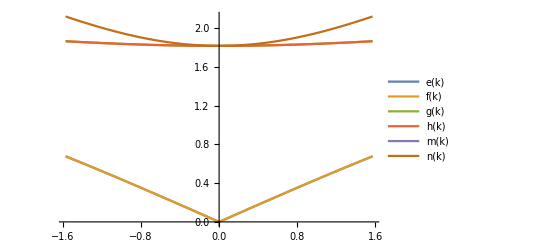

```mathematica
Plot[{e[k],f[k],g[k],h[k],m[k],n[k]},{k,-π/(2a),π/(2a)},PlotLegends->"Expressions"](*gh2个2重根，n1重根*)
```